# Creating a densely-connected deep neural network

## Deep neural networks

Deep leaning is a branch of machine learning.  It is loosely based on the neural structure of the brain, representing layers of connected neurons.
The image below, taken from Wikimedia Common shows a diagram of a neuron.  The cell body is on the left.  It has many dendrites stemming from it.  A long axon terminating in many branches flows from the cell body.  The dendrites connect to the axon terminal ends of many other neurons.  Electrical impulse flow from the dendrites, along the axon.  The impulse is transmitted to dendrites of other neuron on a selected basis.

-Graphics-

A linear regression model can also be viewed as a network of neurons.

-Graphics-

In the image above, the first (vertical layer), represented as three nodes, is the input layer.  Each node carries the value of a variable.  In a spreadsheet file, this might be a row with three entries.  Each entry is in its own column, with each column (header) being one of the three variables.  In machine learning these variables are referred to as feature variables.  The fourth column in this scenario, would be the target variable.  The aim is to use the values of the three feature variable to predict the value of the target variable.

The second layer above represents a hidden layer of three nodes.  A weight, β_i, is multiplied by each feature variable value.  A bias term is added to the sum of  each of the product.  This results in a predicted target value, (ŷ)_i.  This algorithm is termed forward propagation.  During the first run of this forward propagation, random values are selected for the weights and the bias.

The predicted value might be different from the actual value, y_i.  Depending on the type of the target variable, there are a number of ways of calculating the difference between the predicted and the actual value.  This difference is termed the loss function.

All of the sample (rows) in a dataset go through the same algorithm outlined above (forward propagation).  The losses are combined in a cost function.  The cost function is a multivariable function with all the weights and bias value forming the unknowns.

By a process termed backpropagation, the weights  and bias can be updated by gradient descent aimed as minimizing the cost function.  This minimization is done through the calculation of the partial derivative of the cost function with respect to each of the unknowns, a single variable simplification of which is demonstrated below.

-Graphics-

Gradient descent updates the weight and bias values by subtracting the product of a learning rate value and the partial derivative the previous value from the previous value.

This process (of forward propagation and backpropagation algorithms) repeats through many epochs until (hopefully) the values of the unknowns converge to a minimum for the cost function.

A densely-connected deep neural network differs from a linear regression problem by the addition of activation functions for every node in a layer.  This introduces non-linear decision boundaries.  Every node in a layer is also connected to every other node in a prior layer.  The diagram below shows shows an input layer representing 10 feature variables.  The first hidden layer similarly has 10 nodes and a bias node.  This is repeated for a second hidden layer.  The output layer has two nodes.  The total number of unknowns (parameters) in the cost function is (10×10+10)+(10×10+10)+(10×2+2)=242.  This represents a cost function in 242 dimensions.

-Graphics-

The code and description below imports data from a spreadsheet file and creates a deep neural network as a demonstration of the process.  A target variable exists making this a supervised learning problem.  Since the target variable is binary, representing a class, this is further classified as a classification problem.

## Data import

The current notebook directory can be set as the default directory.  This makes importing files from this directory or its subdirectories easier.

```mathematica
SetDirectory[NotebookDirectory[]];
```

Importing a simulated dataset with 29963 samples, 13 feature variables, and a binary target variable encoded as 0 and 1.   There are no column names in the original spreadsheet file.  The dataset contains much overlapping between the target classes making for a very difficult learning.

```mathematica
dataImport=Import["/Users/derekkweku/Desktop/Academics/new/Deep-learning-using-the-Wolfram-Language-master/DCDNNData.csv"];
```

The Dimension[] function can be used to verify the number of rows and columns.

```mathematica
Dimensions[dataImport]
```

{29963,13}

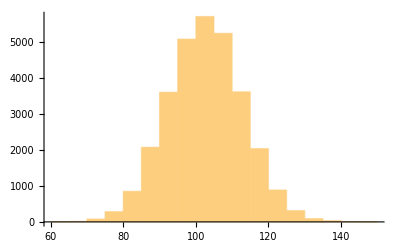
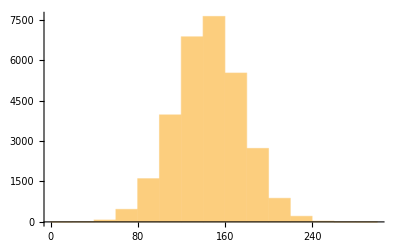
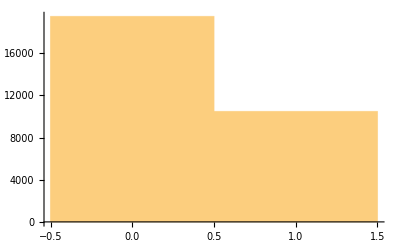
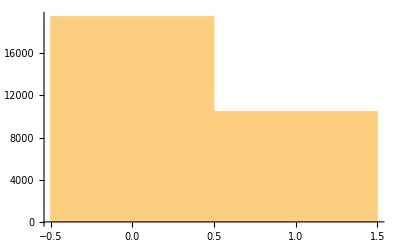
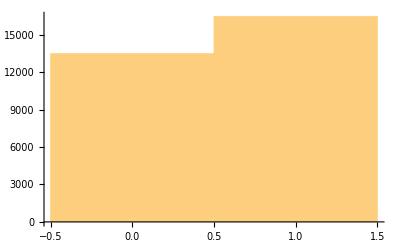
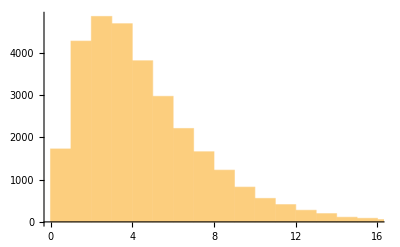
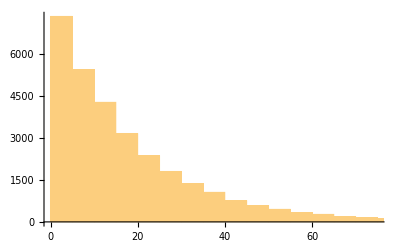
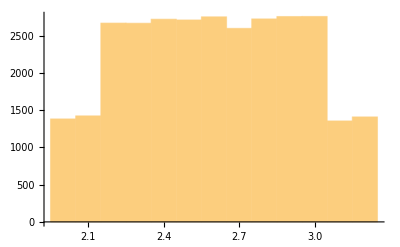

```mathematica
Table[Histogram[dataImport⟦;;,i⟧],{i,12}]
```

## Splitting the data into training and test sets

Setting the number of rows.

```mathematica
n=Length[dataImport]
```

29963

Creating a variable to hold 90% of the data.

```mathematica
trainN=Floor[0.9*n]
```

26966

Given a list (first argument), the TakeDrop[] function selects the first n elements (second argument) and returns it as the first sublist in a list object.  The remainder is placed in a second sublist.  These two sublists can be individually named as separate objects.  By adding the RandomSample[] function, a random selection of rows of similar size, n, is taken as first sublist and the complement is stored in the second sublist.

```mathematica
RandomSeed[123];
{dataTrain,dataTest}=TakeDrop[RandomSample@dataImport,trainN];
Dimensions[dataTrain]
Dimensions[dataTest]
```

{26966,13}

{2997,13}

Create variables to separately hold the feature variables and the target variable for each of the training and test sets.

```mathematica
xTrain=dataTrain⟦All,1;;12⟧;
yTrain=dataTrain⟦All,13⟧;
xTest=dataTest⟦All,1;;12⟧;
yTest=dataTest⟦All,13⟧;
```

Using a histogram to verify the distribution of the target classes.

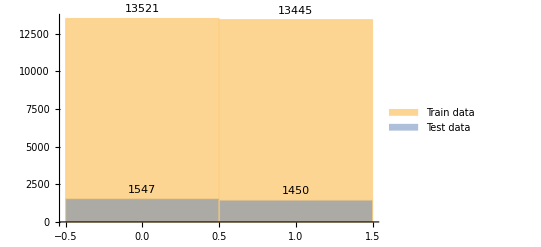

```mathematica
Histogram[{yTrain,yTest},ChartLegends->{"Train data","Test data"},LabelingFunction->Above]
```

## Manipulating the data

Data manipulation starts with transforming the scale of each of the feature variables.  One such method is standardization, shown in equation (1) for the mean and standard deviation for each specific variable (column).

x_i=(x_i-x̄)/σ

The mean of each column is shown below

```mathematica
Mean[xTrain]//N
```

{102.555,145.125,0.350998,0.349663,0.549915,4.48717,17.8758,2.60115,0.348587,9.90197,1010.45,145.343}

The standard deviation for each column is also shown.

```mathematica
StandardDeviation[xTrain]//N
```

{10.2516,30.753,0.477291,0.476872,0.497512,3.02899,18.036,0.333303,0.476532,9.08834,205.928,32.2448}

The Map[] function maps a function to a list object.  The latter must be transposed (as the function maps over rows and not columns) and the result transposed again to recreate the original data dimensions.  The code below shows a mean of 0 and a standard deviation of 1 for each of the variables.

```mathematica
xTrainStandardized=Transpose@Map[Standardize,Transpose[xTrain]];
Mean[xTrainStandardized]
StandardDeviation[xTrainStandardized]
```

{3.25944×10^-16,1.26478×10^-16,0,0,0,-3.26735×10^-17,-1.28718×10^-16,7.7784×10^-16,0,1.37018×10^-17,-4.9748×10^-16,2.14222×10^-16}

{1.,1.,1,1,1,1.,1.,1.,1,1.,1.,1.}

The same transformation must occur for the test data.  However, it is important that the mean and standard deviation of the training data variables be used for the transformation.

```mathematica
xTestStandardized=Transpose@Table[(xTest[[All,i]]-Mean[xTrain][[i]])/StandardDeviation[xTrain][[i]],{i,12}];
```

The mean and standard deviation of the test data variables will not quite be 0 and 1.

```mathematica
Mean[xTestStandardized]//N
StandardDeviation[xTestStandardized]//N
```

{-0.0158128,0.00790263,-0.0293194,0.000742642,-0.004758,0.0126203,0.0117366,-0.000256732,0.0352091,0.0111305,-0.00392656,-0.0153912}

{0.991794,1.00747,0.990517,1.00038,1.00061,0.993347,1.02335,1.0037,1.01066,1.01346,0.986616,1.00717}

A variable called train is created to hold a list of the feature variables and each individual sample target class using the Table[] function to iterate over each sample.

```mathematica
train=Table[xTrainStandardized⟦i,All⟧->yTrain⟦i⟧,{i,trainN}];
Dimensions[train]
train⟦;;1⟧ //N (*Show first sample*)
```

{26966}

{{1.45782,-0.579616,1.35976,-0.733242,-1.10533,-0.656048,2.45532,0.296567,1.36699,-0.93218,-0.077443,0.0420698}→1.}

The same is done for the test set.

```mathematica
test=Table[xTestStandardized⟦i,All⟧->yTest⟦i⟧,{i,Length[yTest]}];
Dimensions[test]
test⟦;;1⟧//N
```

{2997}

{{-0.434577,-1.05762,-0.735395,-0.733242,0.904673,0.33438,-0.248159,-0.00346022,-0.731509,-0.110247,0.855408,0.50726}→0.}

## Creating the neural network

A decoder is created to specify the two classes in the target variable.

```mathematica
dec=NetDecoder[{"Class",{0,1}}]
```

NetDecoder[<>]

Examples of two networks are shown below.

```mathematica
SeedRandom[123]
netOne=NetInitialize[NetChain[{5,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->12],Method->{"Random","Weights"->0.01,"Biases"->0}]
netTwo=NetInitialize[NetChain[{5,Ramp,5,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->12],Method->{"Xavier","FactorType"->"Mean","Distribution"->"Uniform"}]
```

RandomGeneratorState[…]

NetChain[<>]

NetChain[<>]

```mathematica
NetExtract[netOne,{1,"Weights"}]
```

NumericArray[…]

The initial random weight values can be shown.

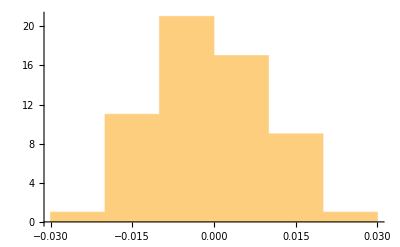

```mathematica
Histogram[Flatten[NetExtract[netOne,{1,"Weights"}]],{0.01}]
```

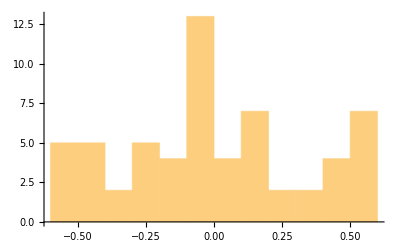

```mathematica
Histogram[Flatten[NetExtract[netTwo,{1,"Weights"}]],{0.1}]
```

Examples are left in comments below (**).

```mathematica
(*trained=NetTrain[netOne,train,BatchSize->256,ValidationSet->test,TargetDevice->"GPU",LossFunction->CrossEntropyLossLayer["Binary"],Method->{"ADAM","Beta1"->0.9,"L2Regularization"->0.1,"LearningRate"->0.0003},MaxTrainingRounds->25]*)
(*trained=NetTrain[netOne,train,BatchSize->256,ValidationSet->test,TargetDevice->"GPU",MaxTrainingRounds->25]*)
trained=NetTrain[netOne,train,BatchSize->256,ValidationSet->test,TargetDevice->"CPU",Method->"SGD",MaxTrainingRounds->25]
```

NetChain[<>]

The first  sample row is passed as an argument to show the predicted target value.

```mathematica
trained[xTestStandardized[[1]]]
```

0

A classifier measurements object can be created.

```mathematica
c=ClassifierMeasurements[trained,test]
```

ClassifierFunction::invindata2: Data supplied to port "Input" was not a length-12 vector (or a list of these).

ClassifierMeasurements[NetChain[<>],{{-0.434577,-1.05762,8,0.855408,0.50726}→0,2995,{1}→0}]
 |  |  |  |

A list of properties for this object can be extracted.

```mathematica
c["Properties"]
```

ClassifierMeasurements[NetChain[<>],{1}][Properties]
 |  |  |  |

Showing the accuracy property.

```mathematica
c["Accuracy"]
```

ClassifierMeasurements[NetChain[<>],{1}][Accuracy]
 |  |  |  |

A confusion matrix plot shows the errors and correct predictions.

```mathematica
c["ConfusionMatrixPlot"]
```

ClassifierMeasurements[NetChain[<>],{1}][ConfusionMatrixPlot]
 |  |  |  |

More of the properties are explored below.

```mathematica
c["Report"]
```

ClassifierMeasurements[NetChain[<>],{1}][Report]
 |  |  |  |

```mathematica
c["AreaUnderROCCurve"]
```

ClassifierMeasurements[NetChain[<>],{1}][AreaUnderROCCurve]
 |  |  |  |

```mathematica
c["ROCCurve"]
```

ClassifierMeasurements[NetChain[<>],{1}][ROCCurve]
 |  |  |  |

```mathematica
c["ClassMeanCrossEntropy"]
```

ClassifierMeasurements[NetChain[<>],{1}][ClassMeanCrossEntropy]
 |  |  |  |